#### Problem 1.

```mathematica
KE={16,32,47,64,80,96,112,128}/1000;
d={0.047,0.10,0.151,0.200,0.251,0.301,0.352,0.402};
m=0.125; g=9.80;
```

| Estimate | Standard Error | t-Statistic | P-Value
X | 0.259933 | 0.000666788 | 389.828 | 1.93019×10^-16

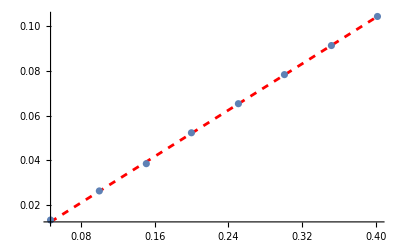

```mathematica
y= KE/(m*g);
data = Thread[{d, y}];
dataplot = ListPlot[data];
fit =LinearModelFit[data, X, X, IncludeConstantBasis->False];
fit["ParameterTable"]
fitplot=Plot[fit[X],{X, Min[d],Max[d]}, PlotStyle->{Red, Dashed}];
Show[fitplot, dataplot]
```

#### Problem 4. Part (a)

| Estimate | Standard Error | t-Statistic | P-Value
v | 8.99831 | 0.016171 | 556.447 | 8.09032×10^-32
cap | 0.0000420104 | 2.09302×10^-7 | 200.716 | 1.27901×10^-25

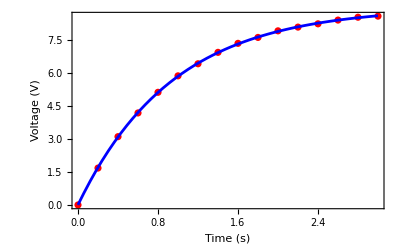

```mathematica
tVals={0.0,0.2,0.4,0.6,0.8,1.0,1.2,1.4,1.6,1.8,2.0,2.2,2.4,2.6,2.8,3.0};
VcVals={0.00,1.68,3.11,4.19,5.13,5.88,6.43,6.95,7.36,7.63,7.93,8.10,8.25,8.42,8.55,8.60};
resistor=22600;
data=Transpose[{tVals,VcVals}];
nlm=NonlinearModelFit[data,v*(1-Exp[-t/(resistor*cap)]),{{v,9.0},{cap,0.0001}},t];
(*results*)
nlm["ParameterTable"]
Show[ListPlot[data,PlotStyle->Red,Frame->True,FrameLabel->{"Time (s)","Voltage (V)"}],Plot[nlm[t],{t,0,3},PlotStyle->Blue]]
```

#### Problem 4(b)

| Estimate | Standard Error | t-Statistic | P-Value
a | 7.76602 | 0.0650122 | 119.455 | 7.94181×10^-20
k | 1.05614 | 0.0143872 | 73.4084 | 2.71684×10^-17

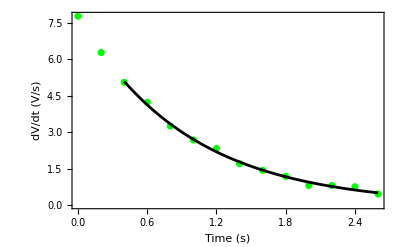

```mathematica
current = Table[(VcVals[[i+2]]-VcVals[[i]])/(2*0.2), {i,1,Length[VcVals]-2}];
t2=Table[tVals[[i]], {i,1,Length[VcVals]-2}];
idata=Thread[{t2,current}];
ifit=NonlinearModelFit[idata,a*Exp[-k*t],{{a,10},{k,0.5}},t];
Print[ifit["ParameterTable"]]
Show[ListPlot[idata,PlotStyle->Green,Frame->True,FrameLabel->{"Time (s)","dV/dt (V/s)"}],Plot[ifit[t],{t,0.4,2.6},PlotStyle->Black]]
```